# Ideal HRG {T,μ_B,μ_Q}-scan

This notebook computes thermodynamic quantities using the hadron resonance gas (HRG) by performing a {T,μ_B,μ_Q}. In the process, we select only the regions

```mathematica
rawDataCopper=Import["/Users/jordi/Library/CloudStorage/Box-Box/Research/papers/2411.03705/thermal-fit-wrapper/output/ANALYSIS=T_muB_muQ_scan_chi2_MODELTYPE=0_DATA=STAR-CuCu200GeV_feeddown_corrected_TIMESTAMP=20251008-233055.csv"];
rawDataGold=Import["/Users/jordi/Library/CloudStorage/Box-Box/Research/papers/2411.03705/thermal-fit-wrapper/output/ANALYSIS=T_muB_muQ_scan_chi2_MODELTYPE=0_DATA=STAR-AuAu200GeV_feeddown_corrected_TIMESTAMP=20251008-210731.csv"];
rawDataUranium=Import["/Users/jordi/Library/CloudStorage/Box-Box/Research/papers/2411.03705/thermal-fit-wrapper/output/ANALYSIS=T_muB_muQ_scan_chi2_MODELTYPE=0_DATA=STAR-UU200GeV_feeddown_corrected_TIMESTAMP=20251009-011950.csv"];
```

```mathematica
(* Remove header *)
dataCopper=Delete[rawDataCopper,1];
dataGold=Delete[rawDataGold,1];
dataUranium=Delete[rawDataUranium,1];
(* Find the minimum of χ^2 for each system *)
minChi2Copper=Min[dataCopper[[All,12]]];
minChi2Gold=Min[dataGold[[All,12]]];
minChi2Uranium=Min[dataUranium[[All,12]]];
(* Find the location of the minima *)
locationMinChi2Copper=First@Select[dataCopper,#[[12]]==minChi2Copper&];
locationMinChi2Gold=First@Select[dataGold,#[[12]]==minChi2Gold&];
locationMinChi2Uranium=First@Select[dataUranium,#[[12]]==minChi2Uranium&];
(* Print information *)
Print["=====> Cu: (χ^2)_min = ",minChi2Copper, " at ", "(T, μ_B, μ_Q) = ", locationMinChi2Copper[[{1,2,4}]]]
Print["=====> Au: (χ^2)_min = ",minChi2Gold, " at ", "(T, μ_B, μ_Q) = ", locationMinChi2Gold[[{1,2,4}]]]
Print["=====>  U: (χ^2)_min = ",minChi2Uranium, " at ", "(T, μ_B, μ_Q) = ", locationMinChi2Uranium[[{1,2,4}]]]
```

=====> Cu: (χ^2)_min = 5.46665 at (T, μ_B, μ_Q) = {147.4,21.5,-1.6}

=====> Au: (χ^2)_min = 2.69482 at (T, μ_B, μ_Q) = {151.5,27.,-3.5}

=====>  U: (χ^2)_min = 3.11339 at (T, μ_B, μ_Q) = {148.5,26.5,-1.9}

```mathematica
(* Create convex hulls *)
chmCopper=ConvexHullMesh[Select[dataCopper,#[[12]]<minChi2Copper+1&]/.{T_,μB_,μS_,μQ_,nB_,nS_,nQ_,baryonDensityOverChargeDensity_,energyDensity_,entropyDensity_,entropyDensityOverBaryonDensity_,chi2_,chi2OverNdof_}->{μQ,μB,T},
MeshCellStyle->{1->None,{2,All}->Opacity[0.1,Red]}];
chmGold=ConvexHullMesh[Select[dataGold,#[[12]]<minChi2Gold+1&]/.{T_,μB_,μS_,μQ_,nB_,nS_,nQ_,baryonDensityOverChargeDensity_,energyDensity_,entropyDensity_,entropyDensityOverBaryonDensity_,chi2_,chi2OverNdof_}->{μQ,μB,T},
MeshCellStyle->{1->None,{2,All}->Opacity[0.1,Blue]}];
chmUranium=ConvexHullMesh[Select[dataUranium,#[[12]]<minChi2Uranium+1&]/.{T_,μB_,μS_,μQ_,nB_,nS_,nQ_,baryonDensityOverChargeDensity_,energyDensity_,entropyDensity_,entropyDensityOverBaryonDensity_,chi2_,chi2OverNdof_}->{μQ,μB,T},
MeshCellStyle->{1->None,{2,All}->Opacity[0.1,Green]}];
```

```mathematica
Show[{
Graphics3D@chmCopper,
Graphics3D@chmGold,
Graphics3D@chmUranium
},
RegionIntersection[
TriangulateMesh@chmCopper,
TriangulateMesh@chmGold,
TriangulateMesh@chmUranium
],
PlotRange->{{-10,5},{10,40},{140,160}},
BoxRatios->{1,1,1},
ViewPoint->{2,-0.9,0.6},
ViewVertical->{0,0,1},
ImageSize->Large,
Axes->True,
AxesLabel->{"μ_Q","μ_B","T"}
]
```

-Graphics3D-

```mathematica
(* Create convex hulls *)
chmCopper=ConvexHullMesh[Select[dataCopper,#[[12]]<minChi2Copper+1&]/.{T_,μB_,μS_,μQ_,nB_,nS_,nQ_,baryonDensityOverChargeDensity_,energyDensity_,entropyDensity_,entropyDensityOverBaryonDensity_,chi2_,chi2OverNdof_}->{μB/T,μQ},
MeshCellStyle->{1->Red,2->Opacity[0.1,Red]}];
chmGold=ConvexHullMesh[Select[dataGold,#[[12]]<minChi2Gold+1&]/.{T_,μB_,μS_,μQ_,nB_,nS_,nQ_,baryonDensityOverChargeDensity_,energyDensity_,entropyDensity_,entropyDensityOverBaryonDensity_,chi2_,chi2OverNdof_}->{μB/T,μQ},
MeshCellStyle->{1->Blue,2->Opacity[0.1,Blue]}];
chmUranium=ConvexHullMesh[Select[dataUranium,#[[12]]<minChi2Uranium+1&]/.{T_,μB_,μS_,μQ_,nB_,nS_,nQ_,baryonDensityOverChargeDensity_,energyDensity_,entropyDensity_,entropyDensityOverBaryonDensity_,chi2_,chi2OverNdof_}->{μB/T,μQ},
MeshCellStyle->{1->Green,2->Opacity[0.1,Green]}];
```

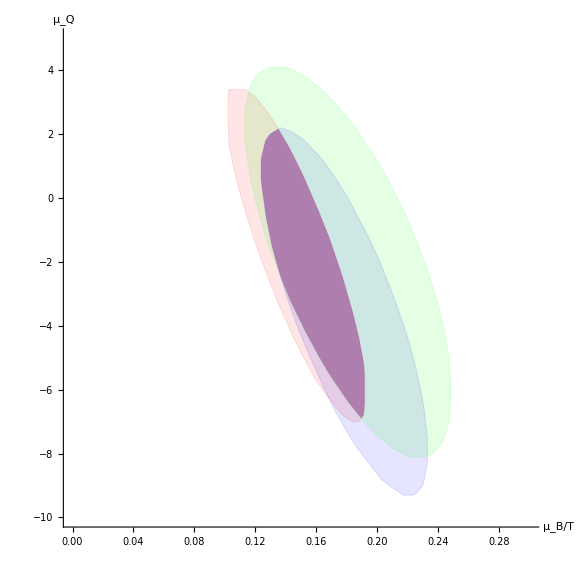

```mathematica
Show[{
Graphics@chmCopper,
Graphics@chmGold,
Graphics@chmUranium
},
Graphics[
{Purple,Opacity[0.4],RegionIntersection[
chmCopper,
chmGold,
chmUranium]
}],
PlotRange->{{0,0.3},{-10,5}},
AspectRatio->1,
ImageSize->Large,
Axes->True,
AxesLabel->{"μ_B/T","μ_Q"}
]
```